```mathematica
PrePots:={
{"N001", 1/2,.015502},
{"N002", .416667,.020864},
{"N003", 1/3,.047142},
{"N004",.229099,.21970},
{"N005", .223607,.0447239},
{"N006", .1666672,.264981},
{"N007", .140063, 5.215756},
{"N008", .117222,13.627636},
{"N009", .125, 23.574089},
{"N010", .089577, 70.120928},
{"N011",.0846258,  158.076937},
{"N012", .0737209, 256.698449},
{"N013", .0932823, 385.280747},
{"N014", .0650034, 615.064615},
{"N015", .0693706, 1036.497657},
{"N016", .0562117,2102.547918},
{"N017", .0769231, 3304.597640},
{"N018", .0548633, 5115.212842},
{"N019", .0630141, 6631.506662},
{"N020", .0393154, 13231.713869},
{"N021", .0460303, 16415.936896},
{"N022", .0412348, 22655.379556},
{"N023", .0389483, 33143.569891},
{"N024", .0354289, 43808.474432},
{"N025", .0343319, 55073.379818},
{"N026", .0276556, 100080.152528},
{"N027", .031485, 114695.203161},
{"N028", .0345975,143321.282072},
{"N029",.038089,165534.223006},
{"N030",.027304,242091.403457},
{"N032", .0251065, 483592.618385},
{"NO34", .0235131, 636943.36965}
}

PottsList:={PrePots[[All,2]]//Flatten,Map[PottsTest2,Take[files,32]],Map[PottsTest3,Take[files,32]],Take[files,32]}//Transpose
```

```mathematica
PottsList//MatrixForm
```

(1/2 | -Graphics3D- | 2 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad001_M2_Inv.dat
0.416667 | -Graphics3D- | 4 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad002_M4_Tetra.dat
1/3 | -Graphics3D- | 6 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad003_M6_Octa.dat
0.229099 | -Graphics3D- | 10 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad004_M10_C4.dat
0.223607 | -Graphics3D- | 12 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad005_M12_Ico.dat
0.166667 | -Graphics3D- | 18 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad006_M18_C4.dat
0.140063 | -Graphics3D- | 22 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad007_M22_C5.dat
0.117222 | -Graphics3D- | 28 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad008_M28_Tetra.dat
0.125 | -Graphics3D- | 32 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad009_M32_Ico.dat
0.089577 | -Graphics3D- | 42 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad010_M42_C4.dat
0.0846258 | -Graphics3D- | 48 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad011_M48_Octa.dat
0.0737209 | -Graphics3D- | 58 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad012_M58_C4.dat
0.0932823 | -Graphics3D- | 64 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad013_M64_Inv.dat
0.0650034 | -Graphics3D- | 72 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad014_M72_Ico.dat
0.0693706 | -Graphics3D- | 82 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad015_M82_C5.dat
0.0562117 | -Graphics3D- | 98 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad016_M98_C4.dat
0.0769231 | -Graphics3D- | 104 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad017_M104_C3.dat
0.0548633 | -Graphics3D- | 122 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad018_M122_C4.dat
0.0630141 | -Graphics3D- | 130 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad019_M130_Inv.dat
0.0393154 | -Graphics3D- | 148 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad020_M148_Tetra.dat
0.0460303 | -Graphics3D- | 156 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad021_M156_C3.dat
0.0412348 | -Graphics3D- | 178 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad022_M178_C4.dat
0.0389483 | -Graphics3D- | 186 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad023_M186_C3.dat
0.0354289 | -Graphics3D- | 210 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad024_M210_C4.dat
0.0343319 | -Graphics3D- | 220 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad025_M220_Inv.dat
0.0276556 | -Graphics3D- | 244 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad026_M244_Tetra.dat
0.031485 | -Graphics3D- | 254 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad027_M254_C3.dat
0.0345975 | -Graphics3D- | 282 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad028_M282_C4.dat
0.038089 | -Graphics3D- | 292 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad029_M292_C5.dat
0.027304 | -Graphics3D- | 322 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad030_M322_C4.dat
0.0251065 | -Graphics3D- | 364 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad032_M364_Tetra.dat
0.0235131 | -Graphics3D- | 410 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad034_M410_C4.dat)

```mathematica
Prepend[PottsList, {"SCD(X)", "X", "|X|", "Filename"}]//MatrixForm
```

(SCD(X) | X | |X| | Filename
1/2 | -Graphics3D- | 2 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad001_M2_Inv.dat
0.416667 | -Graphics3D- | 4 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad002_M4_Tetra.dat
1/3 | -Graphics3D- | 6 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad003_M6_Octa.dat
0.229099 | -Graphics3D- | 10 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad004_M10_C4.dat
0.223607 | -Graphics3D- | 12 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad005_M12_Ico.dat
0.166667 | -Graphics3D- | 18 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad006_M18_C4.dat
0.140063 | -Graphics3D- | 22 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad007_M22_C5.dat
0.117222 | -Graphics3D- | 28 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad008_M28_Tetra.dat
0.125 | -Graphics3D- | 32 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad009_M32_Ico.dat
0.089577 | -Graphics3D- | 42 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad010_M42_C4.dat
0.0846258 | -Graphics3D- | 48 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad011_M48_Octa.dat
0.0737209 | -Graphics3D- | 58 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad012_M58_C4.dat
0.0932823 | -Graphics3D- | 64 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad013_M64_Inv.dat
0.0650034 | -Graphics3D- | 72 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad014_M72_Ico.dat
0.0693706 | -Graphics3D- | 82 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad015_M82_C5.dat
0.0562117 | -Graphics3D- | 98 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad016_M98_C4.dat
0.0769231 | -Graphics3D- | 104 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad017_M104_C3.dat
0.0548633 | -Graphics3D- | 122 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad018_M122_C4.dat
0.0630141 | -Graphics3D- | 130 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad019_M130_Inv.dat
0.0393154 | -Graphics3D- | 148 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad020_M148_Tetra.dat
0.0460303 | -Graphics3D- | 156 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad021_M156_C3.dat
0.0412348 | -Graphics3D- | 178 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad022_M178_C4.dat
0.0389483 | -Graphics3D- | 186 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad023_M186_C3.dat
0.0354289 | -Graphics3D- | 210 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad024_M210_C4.dat
0.0343319 | -Graphics3D- | 220 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad025_M220_Inv.dat
0.0276556 | -Graphics3D- | 244 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad026_M244_Tetra.dat
0.031485 | -Graphics3D- | 254 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad027_M254_C3.dat
0.0345975 | -Graphics3D- | 282 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad028_M282_C4.dat
0.038089 | -Graphics3D- | 292 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad029_M292_C5.dat
0.027304 | -Graphics3D- | 322 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad030_M322_C4.dat
0.0251065 | -Graphics3D- | 364 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad032_M364_Tetra.dat
0.0235131 | -Graphics3D- | 410 | /Users/bozo/Google Drive/Spherical Discrepancy/Potts/PottsQuad/Nquad034_M410_C4.dat)

```mathematica
PottsPlotList:={PottsList.{0,0,1,0},PottsList.{1,0,0,0}}//Transpose
PottsPlotListLog:={Log[PottsList.{0,0,1,0}],Log[#]&@PottsList.{1,0,0,0}}//Transpose//Drop[#,0]&
```

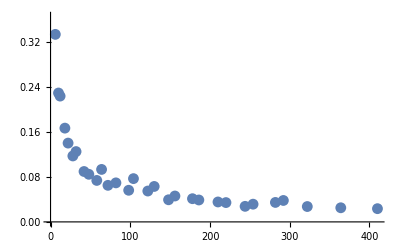

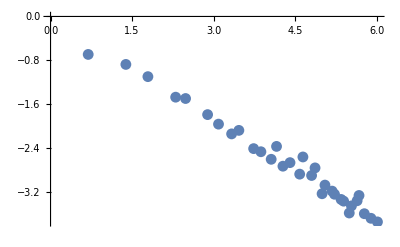

-0.0988172-0.595247 x

```mathematica
ListPlot[PottsPlotList]
ListPlot[PottsPlotListLog]
Fit[PottsPlotListLog,{1,x},x]
```

```mathematica
UniPoint[u_,t_]:={Sqrt[1-u^2]Cos[t],Sqrt[1-u^2]Sin[t],u}
```

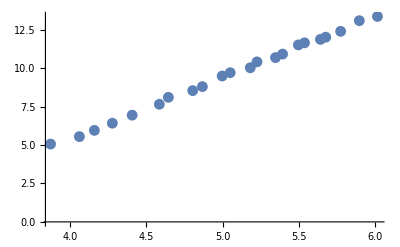

```mathematica
ListPlot[Drop[Log[{Map[PottsTest3,Take[files,32]],PrePots[[All,3]]}]//Transpose,10]]
```

```mathematica
Fit[Drop[Log[{Map[PottsTest3,Take[files,32]],PrePots[[All,3]]}]//Transpose,10],{1,x},x]
```

-10.5834+3.99418 x

```mathematica
TimeSD[y_]:=Exp[-10.5662+4Log[y]]
```

```mathematica
TimeSD[55]
```

235.835